```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Documents\\CNN_Image_network\\data\\Traning_set_resized"]
```

C:\Users\Saesun Kim\Documents\CNN_Image_network\data\Traning_set_resized

```mathematica
data=Import[#]&/@FileNames["*.jpg"];
```

```mathematica
Manipulate[MatrixPlot[ImageData[data[[i]]]],{i,1,Length[data],1}]
```

```mathematica
Table[Floor[ImageData[data[[i]]]*100-1]//Max,{i,1,Length[data]}]
```

{99,99,98,99,99,99,99,98,99,99,98,99,99,99,99,99,96,99,99,99,79,99,99,99,93,98,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,92,99,99,99,99,99,99,99,98,99,98,99,99,99,99,99,99,99,99,99,99,99,99,96,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,97,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,98,99,99,93,99,99,99,99,99,99,99,98,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,89,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,98,99,99,90,99,99,97,99,99,99,91,99,93,96,80,99,99,99,99,99,99,99,99,84,99,99,99,99,94,99,98,99,99,99,99,93,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,92,99,99,99,99,99,95,99,87,99,99,99,79,99,88,99,99,99,99,99,99,99,99,99,98,94,96,99,90,99,99,99,99,99,91,99,99,99,89,99,99,99,99,99,99,99,99,99,99,99,99,92,99,99,99,96,99,99,99,99,86,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,93,95,99,92,99,99,99,99,99,96,99,99,99,95,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99}

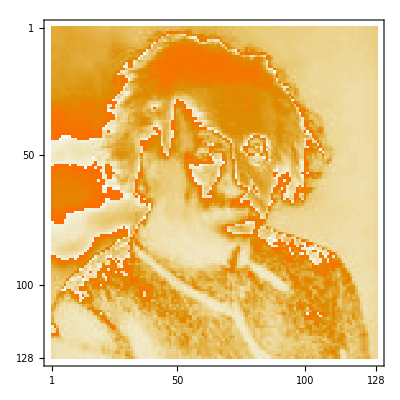

```mathematica
MatrixPlot[Mod[Round[ImageData[data[[1]]]*100],50]]
```

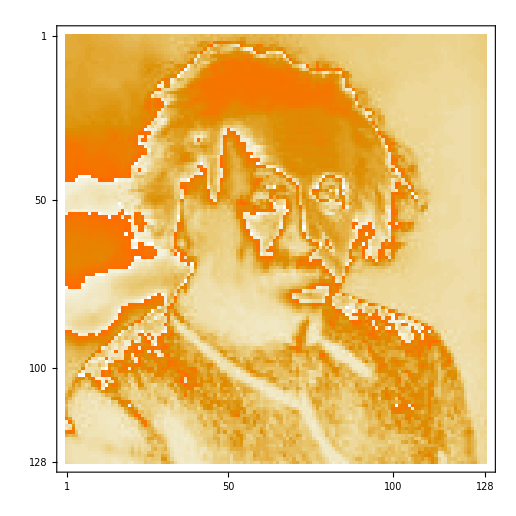
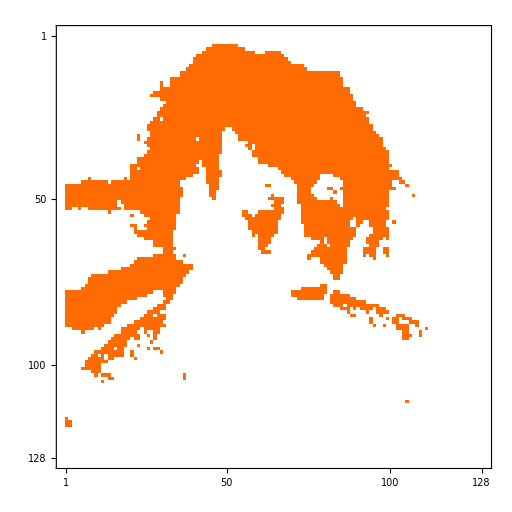

```mathematica
dataorigin=Round[ImageData[data[[1]]]*100-2]
target3fold=Mod[dataorigin,33];
input3data=Table[{i,j,(dataorigin[[i,j]]-target3fold[[i,j]])/33},{i,1,128},{j,1,128}];
target3label=Table[(dataorigin[[i,j]]-target3fold[[i,j]])/33,{i,1,128},{j,1,128}];

target2fold=Mod[dataorigin,50];
input2data=Table[{i,j,(dataorigin[[i,j]]-target2fold[[i,j]])/50},{i,1,128},{j,1,128}];
target2label=Table[(dataorigin[[i,j]]-target2fold[[i,j]])/50,{i,1,128},{j,1,128}];
```

{{22,22,23,23,24,24,24,24,23,23,22,22,22,22,21,20,20,20,19,19,18,18,18,19,20,19,19,19,19,18,18,18,16,17,16,16,16,17,18,18,18,20,18,16,20,18,20,18,19,18,19,21,20,20,22,21,19,22,20,20,21,20,20,19,22,19,19,17,20,17,16,18,15,16,16,15,14,15,15,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,13,12,13,13,12,12,12,12,12,12,11,11,11,11,11,11,11,12,11,11,11,11,11,11,11,10,11,11,12,12,12,13,13,14},127}
 |  |  |  |

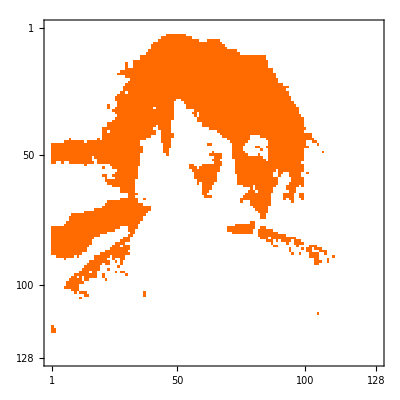

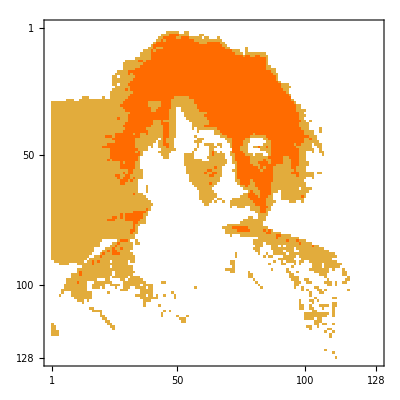

```mathematica
MatrixPlot[target2label]
MatrixPlot[target3label]
```

```mathematica
inputTarget[kk_]:=Module[{dataorigin,target3fold,input3data,target3label,target2fold,input2data,target2label},
dataorigin=Round[ImageData[data[[kk]]]*100-2];
target3fold=Mod[dataorigin,33];
input3data=Table[{i,j,target3fold[[i,j]]},{i,1,128},{j,1,128}];
target3label=Table[(dataorigin[[i,j]]-target3fold[[i,j]])/33,{i,1,128},{j,1,128}];

target2fold=Mod[dataorigin,50];
input2data=Table[{i,j,target2fold[[i,j]]},{i,1,128},{j,1,128}];
target2label=Table[(dataorigin[[i,j]]-target2fold[[i,j]])/50,{i,1,128},{j,1,128}];

{Flatten[input3data,1],Flatten[target3label,1],Flatten[input2data,1],Flatten[target2label,1]}
]
```

```mathematica
inputTargetIm[kk_]:=Module[{dataorigin,target3fold,input3data,target3label,target2fold,input2data,target2label},
dataorigin=Round[ImageData[data[[kk]]]*100-2];
target3fold=Mod[dataorigin,33];
input3data=Table[target3fold[[i,j]]/100,{i,1,128},{j,1,128}];
target3label=Table[(dataorigin[[i,j]]-target3fold[[i,j]])/33,{i,1,128},{j,1,128}];

target2fold=Mod[dataorigin,50];
input2data=Table[target2fold[[i,j]]/100,{i,1,128},{j,1,128}];
target2label=Table[(dataorigin[[i,j]]-target2fold[[i,j]])/50,{i,1,128},{j,1,128}];

{input3data,target3label,input2data,target2label}
]
```

```mathematica
Do[
{input3d,target3l,input2d,target2l}=inputTargetIm[i];
SetDirectory["C:\\Users\\Saesun Kim\\Documents\\CNN_Image_network\\data\\data3fIm"];
Export["input3d"<>ToString[i]<>".jpg",Image[input3d]];
SetDirectory["C:\\Users\\Saesun Kim\\Documents\\CNN_Image_network\\data\\label3fIm"];
Export["target3l"<>ToString[i]<>".jpg",Image[target3l]];
SetDirectory["C:\\Users\\Saesun Kim\\Documents\\CNN_Image_network\\data\\data2fIm"];
Export["input2d"<>ToString[i]<>".jpg",Image[input2d]];
SetDirectory["C:\\Users\\Saesun Kim\\Documents\\CNN_Image_network\\data\\label2fIm"];
Export["target2l"<>ToString[i]<>".jpg",Image[target2l]];
,{i,1,Length[data]}]
```

```mathematica
aList=inputTarget[3][[3]];
colorList=inputTarget[3][[4]]/.{1->Red,0->Black};
bList={#}&/@aList;
ListPointPlot3D[bList,PlotStyle->colorList]
```

-Graphics3D-